```mathematica
ClearAll["Global`*"]
```

```mathematica
tline=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/remesh/solution/test.csv"][[2;;]];
tline=Table[{tline[[i,2]],tline[[i,3]]},{i,2,Length[tline]}]
```

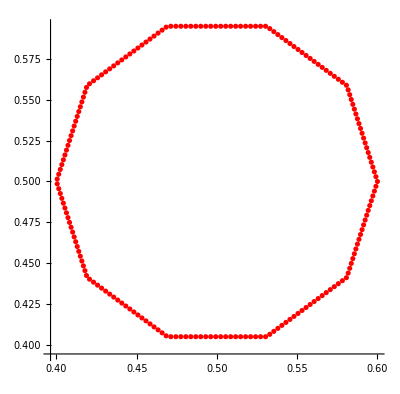

```mathematica
plot1=ListPlot[tline,AspectRatio->Automatic,PlotStyle->Red]
```

{{:0,:1,:2},{0.580902,0.441221,0},{0.542705,0.466921,0},{0.6,0.5,0},{0.530902,0.404894,0},{0.53193,0.51357,0},{0.496084,0.451745,0},{0.469098,0.404894,0},{0.580902,0.558779,0},{0.46022,0.490609,0},{0.48367,0.547404,0},{0.530902,0.595106,0},{0.419098,0.441221,0},{0.419098,0.558779,0},{0.4,0.5,0},{0.469098,0.595106,0}}

{{0.580902,0.441221},{0.542705,0.466921},{0.6,0.5},{0.530902,0.404894},{0.53193,0.51357},{0.496084,0.451745},{0.469098,0.404894},{0.580902,0.558779},{0.46022,0.490609},{0.48367,0.547404},{0.530902,0.595106},{0.419098,0.441221},{0.419098,0.558779},{0.4,0.5},{0.469098,0.595106}}

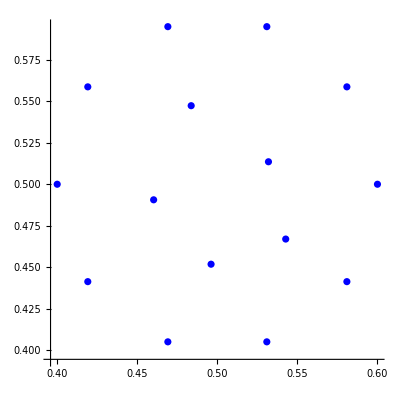

15

```mathematica
tabve=Import["/Users/michelecastellana/Documents/finite_elements/generate_mesh/2d/square/shape_line/solution/mesh_0/sub_meshes/sub_mesh_0/vertices.csv"]
tabve=Table[{tabve[[i,1]],tabve[[i,2]]},{i,2,Length[tabve]}]
plot2=ListPlot[tabve,PlotStyle->Blue,AspectRatio->1]
Length[tabve]
```

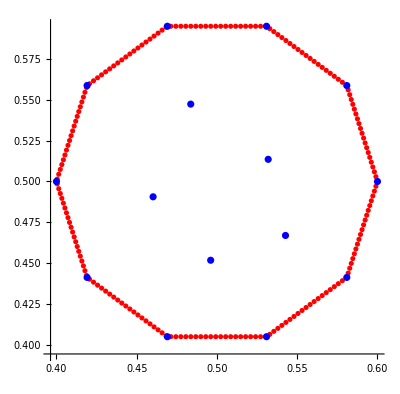

```mathematica
Show[plot1,plot2]
```